```mathematica
以下是能带的计算
```

```mathematica
考虑宇称态,奇宇称,边界连续性方程
```

```mathematica
b=2;w=5;n=3;
Array[ψ,n+1];Array[a,{n+1,2}];
a[1,1]=a[n+1,1]=0;
Do[
If[OddQ[j],ψ[j]=a[j,1] Cos[α x]+a[j,2] Sin[α x],
ψ[j]=a[j,1] ⅇ^(β*x)+a[j,2] ⅇ^(-β*x)],{j,n+1}]
Do[If[j==1,xb=w/2,
xb=xb+(1+(-1)^j)/2 b+(1-(-1)^j)/2 w];
Print[
(D[Log[ψ[j]],x]/.x->xb)==D[Log[ψ[j+1]],x]/.
x->xb],{j,n}]
Clear[n,b,w,a,ψ,xb]
```

1.79067==(0.118548 a[2,1]-0.0741767 a[2,2])/(1.26419 a[2,1]+0.791018 a[2,2])

(0.143003 a[2,1]-0.0614917 a[2,2])/(1.52498 a[2,1]+0.655746 a[2,2])==(-0.933339 a[3,1]+1.22602 a[3,2])/(0.795673 a[3,1]+0.605727 a[3,2])

(-1.3515 a[3,1]-0.740066 a[3,2])/(-0.480295 a[3,1]+0.877107 a[3,2])==-0.0937737

```mathematica
Solve[α Cot[(5 α)/2]==(ⅇ^(5 β/2) β -ⅇ^(-5 β/2) β k[2])/(ⅇ^(5 β/2) +ⅇ^(-5 β/2) k[2]),k[2]]
```

{{k[2]→-1.43913}}

```mathematica
Solve[
((ⅇ^(9 β/2) β -ⅇ^(-9 β/2) β k[2])/(ⅇ^(9 β/2) +ⅇ^(-9 β/2) k[2])/.
k[2]->(ⅇ^(5 β) β-ⅇ^(5 β) α Cot[(5 α)/2])/(β+α Cot[(5 α)/2]))==
(α k[3] Cos[(9 α)/2]-α  Sin[(9 α)/2])/(Cos[(9 α)/2]+k[3] Sin[(9 α)/2]),k[3]]//FullSimplify
```

{{k[3]→1.26954}}

```mathematica
求能量方程,k[j]=a[j,2]/a[j,1]
```

```mathematica
Solve[(α k[3] Cos[(19 α)/2]-α  Sin[(19 α)/2])/(Cos[(19 α)/2]+k[3] Sin[(19 α)/2])==-β,k[3]]
```

{{k[3]→-2.12299}}

```mathematica
最后的方程
```

```mathematica
(2 (1+ⅇ^(4 β)) α β Cos[2 α]+(-1+ⅇ^(4 β)) ((α-β) (α+β) Sin[2 α]+(α^2+β^2) Sin[7 α]))/((-1+ⅇ^(4 β)) (α-β) (α+β) Cos[2 α]+(-1+ⅇ^(4 β)) (α^2+β^2) Cos[7 α]-2 (1+ⅇ^(4 β)) α β Sin[2 α])==(-β Cos[(19 α)/2]+α Sin[(19 α)/2])/(α Cos[(19 α)/2]+β Sin[(19 α)/2])
```

False

```mathematica
长度单位为nm,能量单位为eV,约束方程右边系数
```

```mathematica
(10^-18*2*0.067*9.11*10^-31*1.6*10^-19)/(1.0546*10^-34)^2
```

1.75617

```mathematica
α^2+β^2=1.75617V0
```

Set::write: Tag Plus in 0.0087935  + 2.37425
 is Protected.

2.37961

```mathematica
观察交点
```

```mathematica
V0=1.355;r=1.75617*V0;
equ1=
((2 (1+ⅇ^(4 β)) α β Cos[2 α]+
(-1+ⅇ^(4 β)) 
((α-β) (α+β) Sin[2 α]+(α^2+β^2) Sin[7 α]))/
((-1+ⅇ^(4 β)) (α-β) (α+β) Cos[2 α]+
(-1+ⅇ^(4 β)) (α^2+β^2) Cos[7 α]-
2 (1+ⅇ^(4 β)) α β Sin[2 α])==
(-β Cos[(19 α)/2]+α Sin[(19 α)/2])/(α Cos[(19 α)/2]+β Sin[(19 α)/2]));
equ2=(α^2+β^2==r);
<<Graphics`ImplicitPlot`
ImplicitPlot[{equ1,equ2},{α,0.01,√r},
{β,0.01,√r},PlotPoints->100,
AxesLabel->{"α","β"},AxesOrigin->{0,0},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[V0,r,equ1,equ2]
```

General::obspkg: "Graphics`ImplicitPlot`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

ImplicitPlot[{False,False},{1.54086,0.01,1.5426},{0.0937737,0.01,1.5426},PlotPoints→100,AxesLabel→{α,β},AxesOrigin→{0,0},PlotStyle→Thickness[0.004],AxesStyle→Thickness[0.003]]

```mathematica
求解能量
```

```mathematica
V0=1.355;r=1.75617*V0;
equ1=
((2 (1+ⅇ^(4 β)) α β Cos[2 α]+
(-1+ⅇ^(4 β)) 
((α-β) (α+β) Sin[2 α]+(α^2+β^2) Sin[7 α]))/
((-1+ⅇ^(4 β)) (α-β) (α+β) Cos[2 α]+
(-1+ⅇ^(4 β)) (α^2+β^2) Cos[7 α]-
2 (1+ⅇ^(4 β)) α β Sin[2 α])==
(-β Cos[(19 α)/2]+α Sin[(19 α)/2])/(α Cos[(19 α)/2]+β Sin[(19 α)/2]));
equ2=(α^2+β^2==r);
FindRoot[{equ1,equ2},{α,0.4},{β,1.4}]
FindRoot[{equ1,equ2},{α,0.85},{β,1.2}]
FindRoot[{equ1,equ2},{α,1.4},{β,0.5}]
Clear[V0,r,equ1,equ2]
```

FindRoot::nlnum: The function value {False, False} is not a list of numbers with dimensions {2} at {α, β} = {0.4, 1.4}.

FindRoot[{equ1,equ2},{α,0.4},{β,1.4}]

FindRoot::nlnum: The function value {False, False} is not a list of numbers with dimensions {2} at {α, β} = {0.85, 1.2}.

FindRoot[{equ1,equ2},{α,0.85},{β,1.2}]

FindRoot::nlnum: The function value {False, False} is not a list of numbers with dimensions {2} at {α, β} = {1.4, 0.5}.

FindRoot[{equ1,equ2},{α,1.4},{β,0.5}]

```mathematica
a={0.496861,0.962083,1.42402};
energy=a^2/1.75617
Clear[a,energy]
```

{0.140573,0.527058,1.15469}

```mathematica
搜索方程的根
```

```mathematica
V0=1.355;r=1.75617*V0;tab={};
diff=
(2 (1+ⅇ^(4 β)) α β Cos[2 α]+
(-1+ⅇ^(4 β)) 
((α-β) (α+β) Sin[2 α]+(α^2+β^2) Sin[7 α]))/
((-1+ⅇ^(4 β)) (α-β) (α+β) Cos[2 α]+
(-1+ⅇ^(4 β)) (α^2+β^2) Cos[7 α]-
2 (1+ⅇ^(4 β)) α β Sin[2 α])-(-β Cos[(19 α)/2]+α Sin[(19 α)/2])/(α Cos[(19 α)/2]+β Sin[(19 α)/2]);
Do[η=√(r-ξ^2);If[Abs[(diff/.{α->ξ,β->η})]<10^-4,
AppendTo[tab,{ξ,η}]],{ξ,0.95,1.2,10^-6}]
tab
Clear[V0,r,tab,diff,η]
```

{}

```mathematica
4个能量
```

```mathematica
α={0.496861,0.962083,1.00051,1.42402};
energy=α^2/1.75617
Clear[α,energy]
```

{0.140573,0.527058,0.570002,1.15469}

```mathematica
偶宇称态
```

```mathematica
能量方程
```

```mathematica
(-β Cos[(19 α)/2]+α Sin[(19 α)/2])/(α Cos[(19 α)/2]+β Sin[(19 α)/2])==
((-1+ⅇ^(4 β)) (-α^2+β^2) Cos[2 α]+
(-1+ⅇ^(4 β)) (α^2+β^2) Cos[7 α]+2 (1+ⅇ^(4 β)) α β Sin[2 α])/
(2 (1+ⅇ^(4 β)) α β Cos[2 α]-
(-1+ⅇ^(4 β)) ((-α^2+β^2) Sin[2 α]+(α^2+β^2) Sin[7 α]))
```

(-0.0937737 Cos[(19 α)/2]+α Sin[(19 α)/2])/(α Cos[(19 α)/2]+0.0937737 Sin[(19 α)/2])==(0.455129 (0.0087935-α^2) Cos[2 α]+0.455129 (0.0087935+α^2) Cos[7 α]+0.460453 α Sin[2 α])/(0.460453 α Cos[2 α]-0.455129 ((0.0087935-α^2) Sin[2 α]+(0.0087935+α^2) Sin[7 α]))

```mathematica
观察交点
```

```mathematica
V0=1.355;r=1.75617*V0;
equ1=
((-β Cos[(19 α)/2]+α Sin[(19 α)/2])/(α Cos[(19 α)/2]+β Sin[(19 α)/2])==
((-1+ⅇ^(4 β)) (-α^2+β^2) Cos[2 α]+
(-1+ⅇ^(4 β)) (α^2+β^2) Cos[7 α]+
2 (1+ⅇ^(4 β)) α β Sin[2 α])/
(2 (1+ⅇ^(4 β)) α β Cos[2 α]-
(-1+ⅇ^(4 β)) 
((-α^2+β^2) Sin[2 α]+(α^2+β^2) Sin[7 α])));
equ2=(α^2+β^2==r);
<<Graphics`ImplicitPlot`
ImplicitPlot[{equ1,equ2},{α,0.01,√r},
{β,0.01,√r},PlotPoints->100,
AxesLabel->{"α","β"},AxesOrigin->{0,0},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[V0,r,equ1,equ2]
```

General::obspkg: "Graphics`ImplicitPlot`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

ContourPlot::itraw: Raw object 0.0937737 cannot be used as an iterator.

General::stop: Further output of ContourPlot :: itraw will be suppressed during this calculation.

ImplicitPlot[{(-0.0937737 Cos[(19 α)/2]+α Sin[(19 α)/2])/(α Cos[(19 α)/2]+0.0937737 Sin[(19 α)/2])==(0.455129 (0.0087935-α^2) Cos[2 α]+0.455129 (0.0087935+α^2) Cos[7 α]+0.460453 α Sin[2 α])/(0.460453 α Cos[2 α]-0.455129 ((0.0087935-α^2) Sin[2 α]+(0.0087935+α^2) Sin[7 α])),0.0087935+α^2==2.37961},{α,0.01,1.5426},{0.0937737,0.01,1.5426},PlotPoints→100,AxesLabel→{α,β},AxesOrigin→{0,0},PlotStyle→Thickness[0.004],AxesStyle→Thickness[0.003]]

```mathematica
能量
```

```mathematica
a={0.489577,0.504185,0.980721,1.38836,1.47139};
energy=a^2/1.75617
Clear[a,energy]
```

{0.136482,0.144748,0.547677,1.09758,1.23279}

```mathematica
画能级图
```

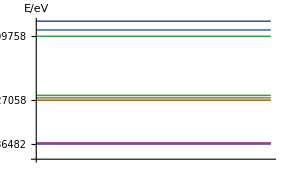

```mathematica
energy={0.136482,0.144748,0.547677,1.09758,
1.23279,0.140573,0.527058,0.570002,1.15469};
Plot[Evaluate[energy],{x,0,1},
Ticks->{None,energy},AxesLabel->"E/eV",
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[energy]
```

```mathematica
1-10个阱的能级分布图
```

```mathematica
计算3个阱情况下的波函数
```

```mathematica
基态,偶宇称
```

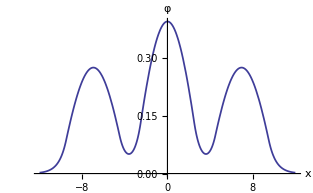

```mathematica
V0=1.355;b=2;w=5;e=0.136482;
U[x_]:=
Which[Abs[x]<w/2,0,w/2<=Abs[x]≤w/2+b,
V0,w/2+b<Abs[x]<3w/2+b,0,
Abs[x]≥3w/2+b,V0];
s=NDSolve[{φ''[x]-1.75617*(U[x]-e)*φ[x]==0,
φ[0]==10,φ'[0]==0},φ,{x,-2w-b,2w+b}];
φ=φ/.s[[1]];
ma=NIntegrate[φ[x]^2,{x,-2w-b,2w+b}];
Plot[φ[x]/√ma,{x,-2w-b,2w+b},
AxesLabel->{"x","φ"},PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[V0,b,w,e,U,s,φ,ma]
```